```mathematica
Ii[j_,k_,m_]:=Integrate[(Cos[δ1-ϕ])^k*(Sin[δ1-ϕ])^m*(ni*Csc[ϕ])^(k+m+2-j)/(k+m+2-j),ϕ,Assumptions->{ϕ∈Reals,δ1∈Reals,ni>0}];
```

```mathematica
Ii100
```

```mathematica
Ii[1,0,0]
```

ni (-Log[2 Cos[ϕ/2]]+Log[2 Sin[ϕ/2]])

```mathematica
d100=FullSimplify[Ii[1,0,0]-ni*Log[Abs[Tan[ϕ/2]]],Assumptions->ni>0]
```

ni (-Log[Abs[Tan[ϕ/2]] Cos[ϕ/2]]+Log[Sin[ϕ/2]])

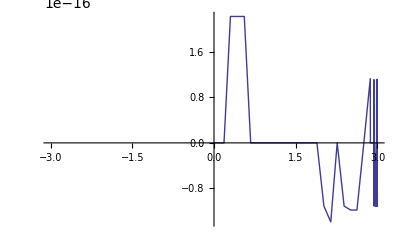

```mathematica
Plot[d100/.ni->1,{ϕ,-3,3}]
```

```mathematica
Ii201
```

```mathematica
Ii[2,0,1]
```

ni (-ϕ Cos[δ1]+Log[Sin[ϕ]] Sin[δ1])

```mathematica
d201=FullSimplify[Ii[2,0,1]+ni*(Sin[δ1]*Log[Abs[Sin[ϕ]]]-ϕ*Sin[δ1]),Assumptions->{ni>0,δ1∈Reals}]
```

ni (-ϕ Cos[δ1]+(-ϕ+Log[Abs[Sin[ϕ]]]+Log[Sin[ϕ]]) Sin[δ1])

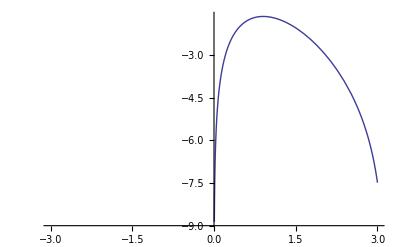

```mathematica
Plot[d201/.{ni->1,δ1->Pi/3},{ϕ,-3,3}]
```

```mathematica
Ii210
```

```mathematica
Ii[2,1,0]
```

ni Cos[δ1] Log[Sin[ϕ]]+ni ϕ Sin[δ1]

```mathematica
Ii311
```

```mathematica
Ii[3,1,1]
```

1/2 ni (2 Cos[ϕ] Sin[2 δ1]-Log[Cos[ϕ/2]] Sin[2 δ1]+Log[Sin[ϕ/2]] Sin[2 δ1]-2 Cos[2 δ1] Sin[ϕ])

```mathematica
Ii302
```

```mathematica
FullSimplify[Ii[3,0,2]]
```

ni (-Cos[2 δ1-ϕ]+(-Log[Cos[ϕ/2]]+Log[Sin[ϕ/2]]) Sin[δ1]^2)

```mathematica
Ii320
```

```mathematica
FullSimplify[Ii[3,2,0]]
```

ni (Cos[2 δ1] Cos[ϕ]+Cos[δ1]^2 (-Log[Cos[ϕ/2]]+Log[-Sin[ϕ/2]])+Sin[2 δ1] Sin[ϕ])

```mathematica
FullSimplify[Cos[2δ1-ϕ]-(Cos[2 δ1] Cos[ϕ]+Sin[2 δ1] Sin[ϕ])]
```

0

```mathematica
FullSimplify[(Cos[2x]+1)-2Cos[x]^2]
```

0